## One Node, Price Boundary

```mathematica
OneNodeSol = Solve[{
pB== -γ (xB - zBC),
ζ zBC == - pB
},{pB,zBC}]
```

{{pB→-(xB γ ζ)/(γ+ζ),zBC→(xB γ)/(γ+ζ)}}

```mathematica
{{pB->-(xB γ ζ)/(γ+ζ),zBC->(xB γ)/(γ+ζ)}}
```

{{pB→-(xB γ ζ)/(γ+ζ),zBC→(xB γ)/(γ+ζ)}}

```mathematica
OneNodePriceVar = (Coefficient[pB/.OneNodeSol,xB])^2
```

{(γ^2 ζ^2)/(γ+ζ)^2}

## Two Nodes, Price Boundary

```mathematica
TwoNodesSol = Solve[{
pB== -γ(xB+zAB-zBC),
pA == -γ (xA-zAB),
ζ zBC == -pB,
ζ zAB == pB - pA 
},{pA, pB, zBC,zAB}]
```

{{pA→-(2 xA γ^2 ζ+xB γ^2 ζ+xA γ ζ^2)/(γ^2+3 γ ζ+ζ^2),pB→-(xA γ^2 ζ+xB γ^2 ζ+xB γ ζ^2)/(γ^2+3 γ ζ+ζ^2),zBC→-(-xA γ^2-xB γ^2-xB γ ζ)/(γ^2+3 γ ζ+ζ^2),zAB→-(-xA γ^2-xA γ ζ+xB γ ζ)/(γ^2+3 γ ζ+ζ^2)}}

```mathematica
TwoNodePriceGap=Simplify[pA-pB/.TwoNodesSol]
```

{-(γ ζ (-xB ζ+xA (γ+ζ)))/(γ^2+3 γ ζ+ζ^2)}

```mathematica
TwoNodePriceVar = Simplify[(Coefficient[TwoNodePriceGap,xA])^2+(Coefficient[TwoNodePriceGap,xB])^2]
```

{(γ^2 ζ^2 (γ^2+2 γ ζ+2 ζ^2))/((γ^2+3 γ ζ+ζ^2)^2)}

## Comparison

```mathematica
PriceVarRatio = Simplify[TwoNodePriceVar/OneNodePriceVar ]
```

{((γ+ζ)^2 (γ^2+2 γ ζ+2 ζ^2))/((γ^2+3 γ ζ+ζ^2)^2)}

```mathematica
Diff = Simplify[Numerator[PriceVarRatio] - Denominator[PriceVarRatio]]
```

{ζ (-2 γ^3-4 γ^2 ζ+ζ^3)}

```mathematica
Simplify[Diff/γ/.ζ->r γ]
```

{r (-2-4 r+r^3) γ^3}

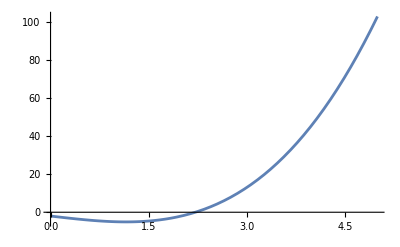

```mathematica
Plot[-2-4 r+r^3,{r,0,5}]
```

```mathematica
Solve[-2-4 r+r^3==0,r]
```

{{r→Root-1.68Root[-2-4 #1+#1^3&,1]-1.6751308705666461},{r→Root-0.539Root[-2-4 #1+#1^3&,2]-0.5391888728108892},{r→Root2.21Root[-2-4 #1+#1^3&,3]2.2143197433775352}}

## Two Price Boundaries

```mathematica
TwoNodesConnPriceSol = Solve[{
pB== -γ(xB+zAB-zBC),
pA == -γ (xA-zAB-zAC),
ζ zBC == -pB,
ζ zAB == pB - pA ,
ζ zAC == - pA 
},{pA, pB, zBC,zAB,zAC}]
```

{{pA→-(2 xA γ^2 ζ+xB γ^2 ζ+xA γ ζ^2)/(3 γ^2+4 γ ζ+ζ^2),pB→-(xA γ^2 ζ+2 xB γ^2 ζ+xB γ ζ^2)/(3 γ^2+4 γ ζ+ζ^2),zBC→-(-xA γ^2-2 xB γ^2-xB γ ζ)/(3 γ^2+4 γ ζ+ζ^2),zAB→-(-xA γ+xB γ)/(3 γ+ζ),zAC→-(-2 xA γ^2-xB γ^2-xA γ ζ)/(3 γ^2+4 γ ζ+ζ^2)}}

```mathematica
Simplify[(3 γ^2+4 γ ζ+ζ^2)/(3 γ+ζ)]
```

γ+ζ

```mathematica
TwoNodeConnPriceGap=Simplify[pA-pB/.TwoNodesConnPriceSol]
```

{((-xA+xB) γ ζ)/(3 γ+ζ)}

```mathematica
TwoNodeConnPriceVar = Simplify[(Coefficient[TwoNodeConnPriceGap,xA])^2+(Coefficient[TwoNodeConnPriceGap,xB])^2]
```

{(2 γ^2 ζ^2)/(3 γ+ζ)^2}

```mathematica
ConnDiff = TwoNodePriceVar-TwoNodeConnPriceVar
```

{-(2 γ^2 ζ^2)/(3 γ+ζ)^2+(γ^2 ζ^2 (γ^2+2 γ ζ+2 ζ^2))/((γ^2+3 γ ζ+ζ^2)^2)}

```mathematica
ConnDiff =Simplify[Together[-(2 γ^2 ζ^2)/(3 γ+ζ)^2+(γ^2 ζ^2 (γ^2+2 γ ζ+2 ζ^2))/((γ^2+3 γ ζ+ζ^2)^2)]]
```

(γ^3 ζ^2 (7 γ^3+12 γ^2 ζ+9 γ ζ^2+2 ζ^3))/((3 γ+ζ)^2 (γ^2+3 γ ζ+ζ^2)^2)

```mathematica
TeXForm[ConnDiff]
```

\frac{\gamma ^3 \zeta ^2 \left(7 \gamma ^3+12 \gamma ^2 \zeta +9 \gamma  \zeta ^2+2 \zeta ^3\right)}{(3 \gamma +\zeta )^2 \left(\gamma ^2+3 \gamma  \zeta +\zeta ^2\right)^2}

```mathematica
ConnRatio2 = Simplify[TwoNodeConnPriceVar/TwoNodePriceVar]
```

{(2 (γ^2+3 γ ζ+ζ^2)^2)/((3 γ+ζ)^2 (γ^2+2 γ ζ+2 ζ^2))}

```mathematica
ConnRatio2r = Simplify[ConnRatio2/.ζ->r γ]
```

{(2 (1+3 r+r^2)^2)/((3+r)^2 (1+2 r+2 r^2))}

```mathematica
Solve[ConnRatio2r==1,r]
```

{{r→Root-2.81Root[7+12 #1+9 #1^2+2 #1^3&,1]-2.806443932358772},{r→Root-0.847-0.728 ⅈRoot[7+12 #1+9 #1^2+2 #1^3&,2]-0.8467780338206138},{r→Root-0.847+0.728 ⅈRoot[7+12 #1+9 #1^2+2 #1^3&,3]-0.8467780338206138}}

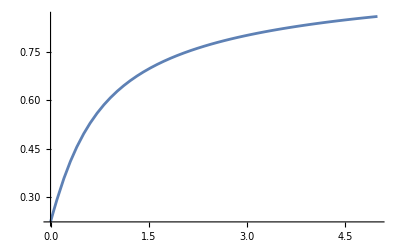

```mathematica
Plot[(2 (1+3 r+r^2)^2)/((3+r)^2 (1+2 r+2 r^2)),{r,0,5}]
```

```mathematica
ConnRatio1 = Simplify[TwoNodeConnPriceVar/OneNodePriceVar]
```

{(2 (γ+ζ)^2)/(3 γ+ζ)^2}

```mathematica
ConnDiff1 = Simplify[Numerator[ConnRatio1] - Denominator[ConnRatio1]]
```

{-7 γ^2-2 γ ζ+ζ^2}

```mathematica
Simplify[ConnDiff1/γ/.ζ->r γ]
```

{(-7-2 r+r^2) γ}

```mathematica
Solve[-7-2 r+r^2==0,r]
```

{{r→1-2 √2},{r→1+2 √2}}

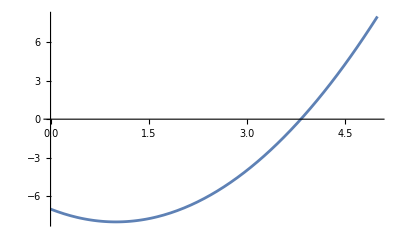

```mathematica
Plot[-7-2 r+r^2,{r,0,5}]
```